```mathematica
Module[{l, length =20},
l = Table[(length-Abs[x-y])/length,{x,0,length},{y,0,length}];
GraphicsRow[{
ListPlot3D[l],
Text[N[Total[l,2]/length^2]]
},ImageSize->Full]
]
```

-Graphics-

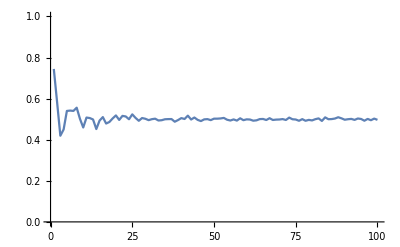

```mathematica
ListLinePlot[
Table[Module[{l,m},
l = Table[(length-Abs[x-y]),{x,1,length},{y,1,length}];
m = Table[Abs[RandomReal[]],{x,1,length},{y,1,length}];
N[Total[l m,2]]/Total[l,2]
],
{length,1,100}],
PlotRange->{0,1}
]
```